Ivan Lakovic

```mathematica
Det[{{2,2,3},{6,5,6},{1,1,2}}]
```

-1

```mathematica
Inverse[{{2,2,3},{6,5,6},{1,1,2}}]
```

{{-4,1,3},{6,-1,-6},{-1,0,2}}

```mathematica
Det[{{-4,1,3},{6,-1,-6},{-1,0,2}}]
```

-1

```mathematica
LUDecomposition[{{2,2,3},{6,5,6},{1,1,2}}]
```

{{{1,1,2},{6,-1,-6},{2,0,-1}},{3,2,1},1}

```mathematica
Orthogonalize[{{2,2,3},{6,5,6},{1,1,2}}]
```

{{2/(√17),2/(√17),3/(√17)},{22/(7 √17),5/(7 √17),-18/(7 √17)},{3/7,-6/7,2/7}}

```mathematica
Det[{{2/(√17),2/(√17),3/(√17)},{22/(7 √17),5/(7 √17),-18/(7 √17)},{3/7,-6/7,2/7}}]
```

-1

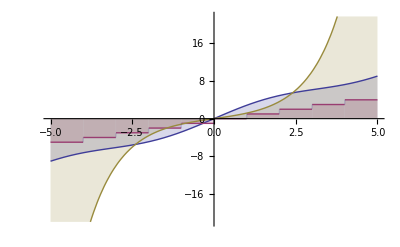

```mathematica
Plot[{Sin[x]+2x,Floor[x],Sinh[x]},{x,-5,5}, Filling->Axis]
```

```mathematica
Plot3D[{-2,Sin[x],x},{x,-4,4},{y,-2,2},PlotStyle->Directive[RGBColor[0.27,1.,0.4],Opacity[0.878]]]
```

-Graphics3D-

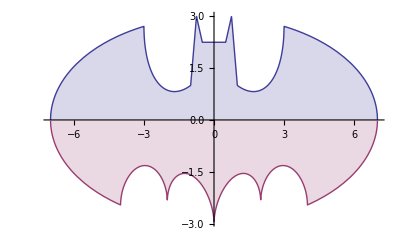

```mathematica
Plot[{With[{
w=3*Sqrt[1-(x/7)^2], 
l=(6/7)*Sqrt[10]+(3+x)/2-(3/7)*Sqrt[10]*Sqrt[4-(x+1)^2],  h=(1/2)*(3*(Abs[x-1/2]+Abs[x+1/2]+6)-11*(Abs[x-3/4]+Abs[x+3/4])),  r=(6/7)*Sqrt[10]+(3-x)/2-(3/7)*Sqrt[10]*Sqrt[4-(x-1)^2]},  w+(l-w)*UnitStep[x+3]+(h-l)*UnitStep[x+1]+(r-h)*UnitStep[x-1]+(w-r)*UnitStep[x-3]],(1/2)*(3*Sqrt[1-(x/7)^2]+Sqrt[1-(Abs[Abs[x]-2]-1)^2]+Abs[x/2]-((3*Sqrt[33]-7)/112)*x^2-3)*((x+4)/Abs[x+4]-(x-4)/Abs[x-4])-3*Sqrt[1-(x/7)^2]},{x,-7,7},Filling->Axis]
```

```mathematica
Formule za znak preuzete su sa http://mathworld.wolfram.com/BatmanCurve.html
```

```mathematica
DSolve[y'[x]==y[x]*e^x,y[x],x]
```

{{y[x]→ⅇ^(e^x/Log[e]) C[1]}}

```mathematica
{{y[x]->ⅇ^(e^x/Log[e]) C[1]}}⟦1,1,2⟧
```

ⅇ^(e^x/Log[e]) C[1]

```mathematica
DSolve[y'[x]==y[x]+e^x,y[x],x]
```

{{y[x]→ⅇ^x C[1]+e^x/(-1+Log[e])}}

```mathematica
{{y[x]->ⅇ^x C[1]+e^x/(-1+Log[e])}}⟦1,1,2⟧
```

ⅇ^x C[1]+e^x/(-1+Log[e])